```mathematica
u=(-ⅇ^(3 ⅈ ξ)+ⅇ^(4 ⅈ ξ))/(d+(5/12-3 d) ⅇ^(ⅈ ξ)+(-4/3+3 d) ⅇ^(2 ⅈ ξ)+(23/12-d) ⅇ^(3 ⅈ ξ));
```

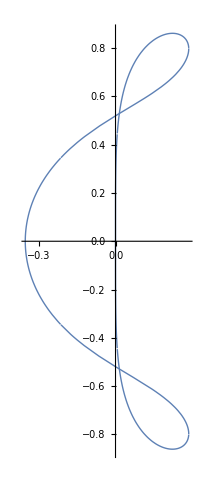

```mathematica
d=-0.25;
p1=ParametricPlot[{Re[u],Im[u]}
,{ξ,0,2π}
,PlotStyle->Thick
,AxesOrigin->{0,0}
,PlotRange->All]
```

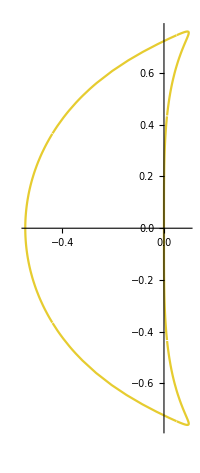

```mathematica
d=0;
p2=ParametricPlot[{Re[u],Im[u]}
,{ξ,0,2π}
,PlotStyle->RGBColor[0.9,0.8,0.19]
,AxesOrigin->{0,0}
,PlotRange->All]
```

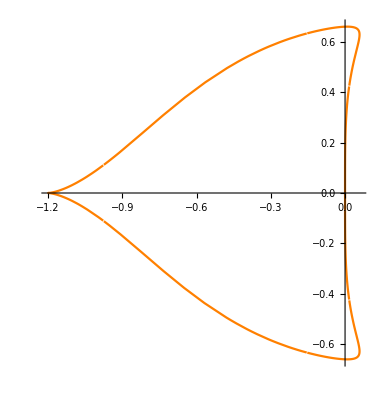

```mathematica
d=0.25;
p3=ParametricPlot[{Re[u],Im[u]}
,{ξ,0,2π}
,PlotStyle->Orange
,AxesOrigin->{0,0}
,PlotRange->All]
```

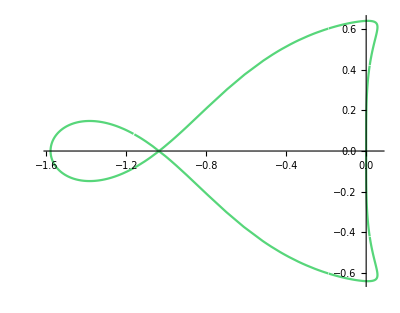

```mathematica
d=0.3;
p4=ParametricPlot[{Re[u],Im[u]}
,{ξ,0,2π}
,PlotStyle->RGBColor[0.34,0.84,0.48]
,AxesOrigin->{0,0}
,PlotRange->All]
```

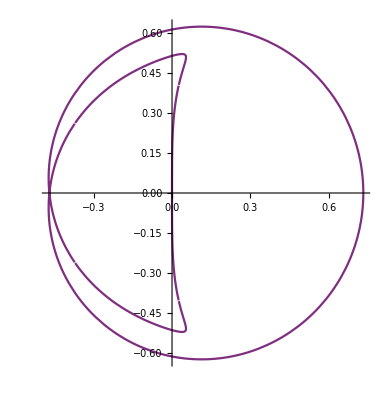

```mathematica
d=0.8;
p5=ParametricPlot[{Re[u],Im[u]}
,{ξ,0,2π}
,PlotStyle->RGBColor[0.5,0.18,0.5]
,AxesOrigin->{0,0}
,PlotRange->All]
```

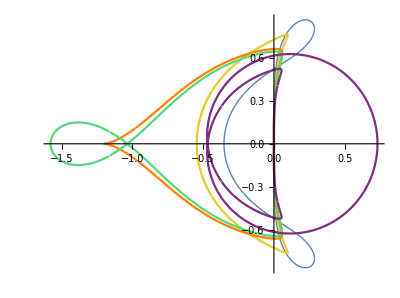

```mathematica
Show[p1,p2,p3,p4,p5]
```

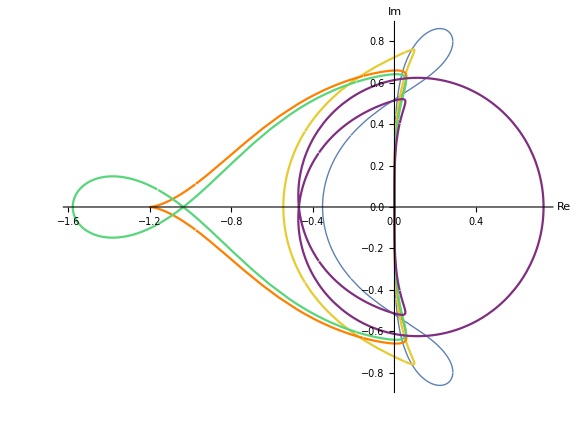

```mathematica
Show[%69,ImageSize->Large,AxesLabel->{Style[Re,Medium],Style[Im,Medium]},AxesStyle->{{Arrowheads[0.03],AbsoluteThickness[1]}, {Arrowheads[0.03],AbsoluteThickness[1]}}]
```

```mathematica
Show[%76,PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```